```mathematica
zeta[s_,n_]:= Sum[1/j^s,{j,1,n}];
```

```mathematica
Zeta[2+2I]//N
```

0.867352-0.275127 ⅈ

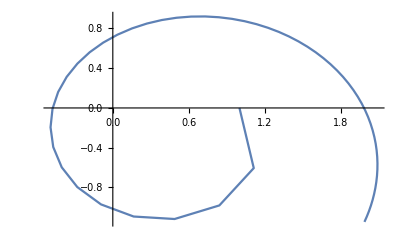

```mathematica
ListPlot[ReIm/@Table[zeta[.7+2 I,k] ,{k,1,60}],Joined->True,AxesOrigin->{0,0}]
```

```mathematica
Zeta[1+2I]//N
```

0.598166-0.351855 ⅈ

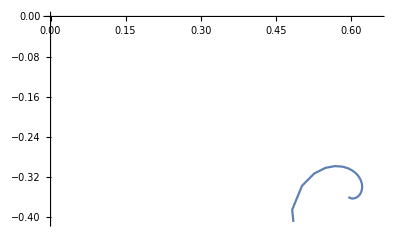

```mathematica
ListPlot[ReIm/@Table[zeta[s,k] - k^(1-s)/(1-s)/.s->1+2I,{k,1,60}],Joined->True,AxesOrigin->{0,0}]
```

```mathematica
ZetaZero[1]//N
```

0.5+14.1347 ⅈ

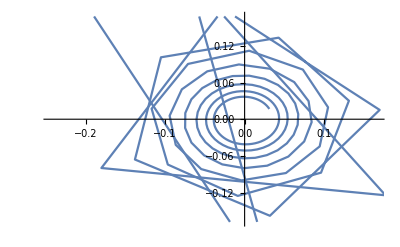

```mathematica
ListPlot[ReIm/@Table[zeta[s,k] - k^(1-s)/(1-s)/.s->0.5+14.134725141734695 ⅈ,{k,1,200}],Joined->True,AxesOrigin->{0,0}]
```

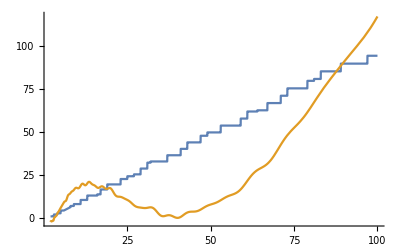

```mathematica
cheb[n_]:=Sum[MangoldtLambda[j],{j,1,n}];
Plot[{cheb[x], x-Log[2Pi]-Sum[(x^ZetaZero[j]/ZetaZero[j] + x^(1-ZetaZero[j])/(1-ZetaZero[j])),{j,1,10}]
-(x^rho/rho + x^(1-rho)/(1-rho)+x^Conjugate[rho]/Conjugate[rho] + x^(1-Conjugate[rho])/(1-Conjugate[rho]))/.rho->1+2I},{x,2,100}]
```

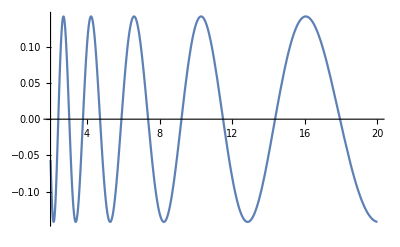

```mathematica
Plot[(x^ZetaZero[1]/ZetaZero[1] + x^(1-ZetaZero[1])/(1-ZetaZero[1]))/x^.5,{x,2,20}]
```

```mathematica
1/(n-1)! d/ds^(n-1)[(s^n)f[s]]|s_>0 = a_[-n]+a_[-n+1]/s^1+...+a_[-1]s^(n-1)+a_0 s^n+a1 s+..
```